### a)

```mathematica
M = {{sigma+1,3},{-2,sigma-1}};
Eigenvalues[M]
```

{-ⅈ √5+sigma,ⅈ √5+sigma}

### b)

```mathematica
x0 = u;
y0 = v;
sol[x0_,y0_]:=DSolve[{x'[t] ==((sigma+1)*x[t]+3y[t]) , y'[t] ==(-2*x[t]+(sigma-1)y[t]), x[0]==x0,y[0]==y0},{x,y},{t}];
sol[x0,y0]
```

{{x→Function[{t},1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])],y→Function[{t},-1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])]}}

### c)

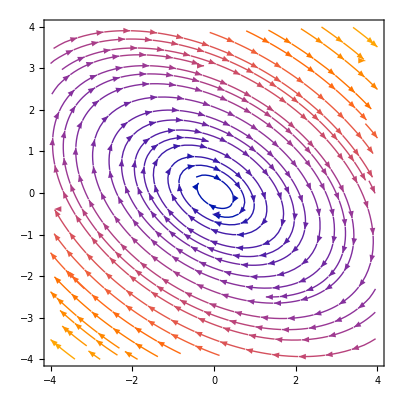

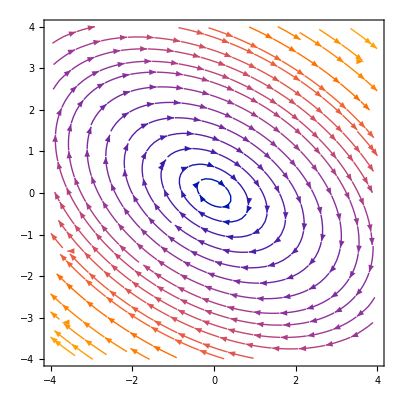

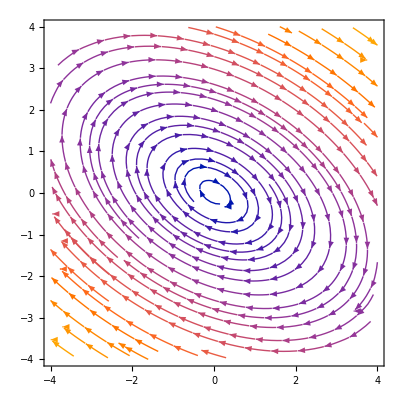

```mathematica
plot1 =StreamPlot[{(σ+ 1)x + 3y, -2x + (σ-1)y} /. {σ -> -1/10},{x,-4,4},{y,-4,4}];
plot2 = StreamPlot[{(σ+ 1)x + 3y, -2x + (σ-1)y} /. {σ -> 0},{x,-4,4},{y,-4,4}];
plot3 = StreamPlot[{(σ+ 1)x + 3y, -2x + (σ-1)y} /. {σ -> 1/10},{x,-4,4},{y,-4,4}];
Show[plot1]
Show[plot2]
Show[plot3]
```

### d)

```mathematica
--
```

### e)

```mathematica
--
```

### f)

```mathematica
--
```